```mathematica
Clear[L]
L=5;

Lt=2L;

Clear[sp,sm,sz,spsm,d]
sp=SparseArray[1/2(PauliMatrix[1]+ⅈ PauliMatrix[2])];
sm=sp†;
sz=SparseArray[PauliMatrix[3]];
spsm=sp.sm;
d=Length[sp];

Clear[n,jw,Sp]
i0=SparseArray[IdentityMatrix[d^Lt]];
jw[1]=i0;
Do[
IL=SparseArray[IdentityMatrix[d^(i-1)]];
IR=SparseArray[IdentityMatrix[d^(Lt-i)]];
Sm[i]=KroneckerProduct[IL,sm,IR];
n[i]=KroneckerProduct[IL,spsm,IR];
jw[i+1]=jw[i].KroneckerProduct[IL,-sz,IR];
,{i,Lt}]

Clear[c]
Do[
c[i]=jw[i].Sm[i];
,{i,0,Lt}]
```

```mathematica
(* checking anticommutation relations *)
DeleteDuplicates[Table[c[i].c[i]†+c[i]†.c[i]==i0,{i,Lt}]]
DeleteDuplicates[Flatten[Table[c[i].c[j]†+c[j]†.c[i]==0*i0,{i,Lt},{j,i+1,Lt}]]]
DeleteDuplicates[Flatten[Table[c[i].c[j]†+c[j]†.c[i]==0*i0,{i,Lt},{j,i-1}]]]
(* checking JW string convention *)
Clear[l]
DeleteDuplicates[Table[jw[l]==SparseArray[DiagonalMatrix[Exp[Diagonal[ⅈ π Sum[n[k],{k,1,l-1}]]]]],{l,2,L}]]
```

{True}

{True}

{True}

«1 more identical outputs»

```mathematica
(*(* introduce a/b sublattice *)
Clear[a,b]
Do[
a[i+1]=c[2i+1];
b[i+1]=c[2i+2];
,{i,0,L-1}]
Clear[ℋ]
ℋ[t_,γ_]:=∑_(i=1)^L ((t+γ/2)a[i]†.b[i]+(t-γ/2)b[i]†.a[i]) ;*)
```

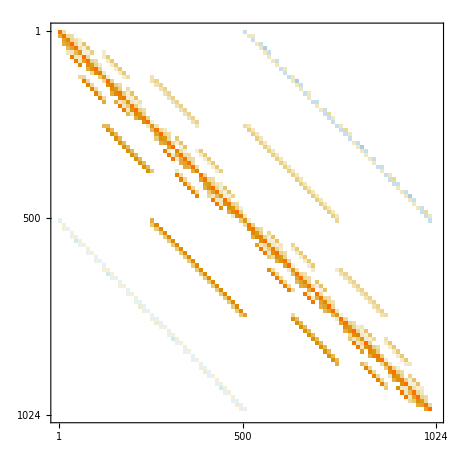

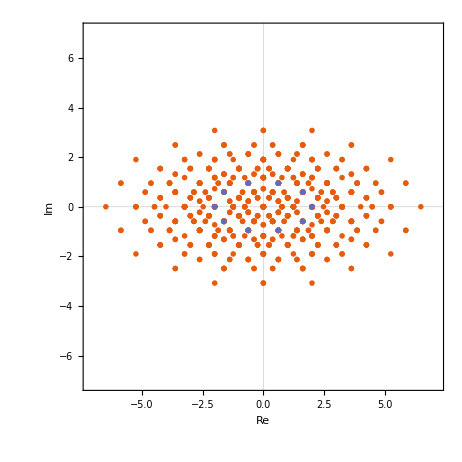

```mathematica
pbc=1;
Clear[ℋ]
c[Lt+1]=pbc*c[1];
ℋ[t_,g_]:=∑_(i=1)^Lt ((t+g)c[i+1]†.c[i]+(t-g)c[i]†.c[i+1])
Clear[g,t,Ham,tr,bl]
{tr,bl} ={ConstantArray[0,{Lt,Lt}], ConstantArray[0,{Lt,Lt}]};
tr[[1,Lt]]=1;bl[[Lt,1]]=1;
Ham[t_,g_]:=DiagonalMatrix[Table[t-g,{i,Lt-1}],1]+DiagonalMatrix[Table[t+g,{i,Lt-1}],-1]+pbc*(t+g)tr+pbc*(t-g)bl;

tt=1.0;gg=0.5;
Hfull=ℋ[tt,gg];
{val1,vec1}=Eigensystem[Normal[Hfull]];
Hsp=Ham[tt,gg];
{val2,vec2}=Eigensystem[Hsp];
Hfull//MatrixPlot
ListPlot[{ReIm@val1,ReIm@val2},PlotMarkers->"OpenMarkers",PlotTheme->"Scientific",AspectRatio->1,PlotRange->1.1Max[Abs[val1]]{{-1,1},{-1,1}},FrameLabel->{"Re", "Im"}]
```